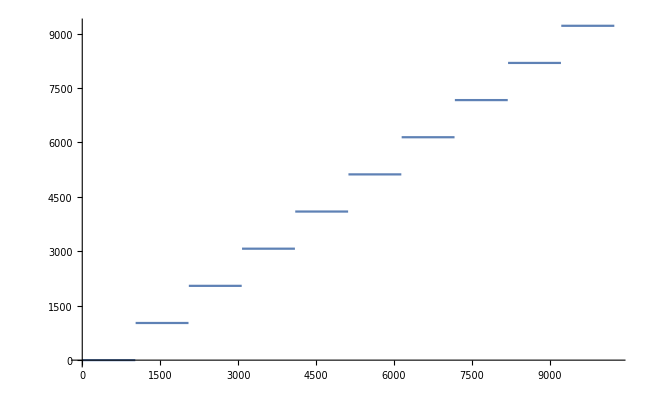

```mathematica
Plot[Min[x,x-Mod[x+1024,1024]],{x, 0, 1024*10}]
```

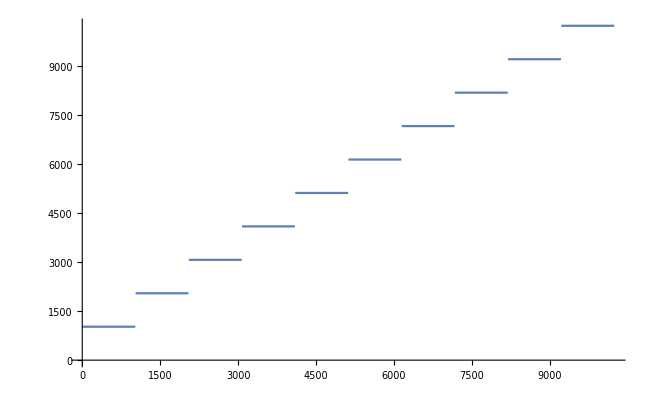

```mathematica
Plot[Max[x,x+Mod[1024-x,1024]],{x, 0, 1024*10}]
```

```mathematica
Mod[1024-4095,1024]
```

1

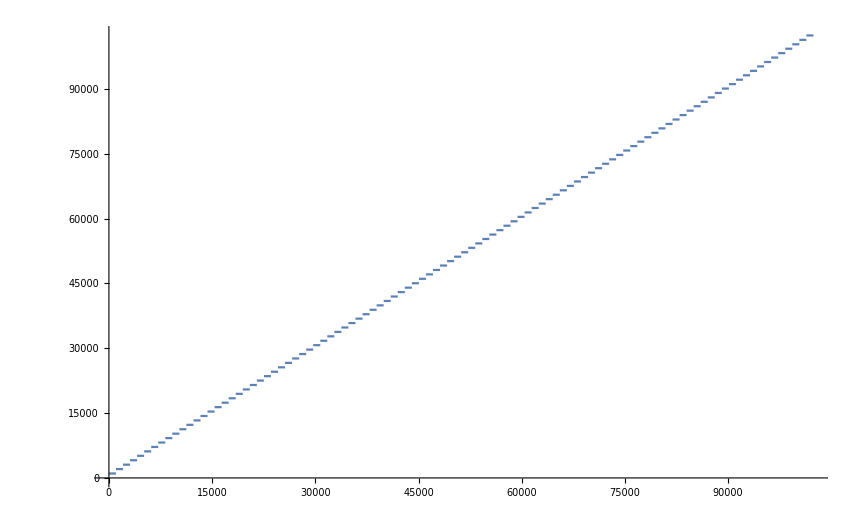

```mathematica
Plot[Max[x,x+Mod[1024-x,1024]],{x, 0, 1024*100},PlotPoints->1000]
```

```mathematica
RoundUpToNearest[n,d]:= Ceiling[n/d]*d
```

```mathematica
Plot[RoundUpToNearest[n,(1024*1024)],{n,0,1024*1024*100},PlotPoints->1000]
```

-Graphics-